```mathematica
dir="/Users/julian/Dropbox/Research/17/Halo_Bias_Code/Neutrinos_Modified/CAMB_Current/output_test/";
```

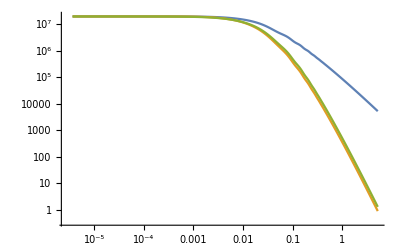

```mathematica
TkC=Import[dir<>"nuFS1_transfer_out_z0.dat","Data"][[;;,{1,2}]];
Tknu=Import[dir<>"nuFS1_transfer_out_z0.dat","Data"][[;;,{1,6}]];
koverhtab=Import[dir<>"nuFS1_transfer_out_z0.dat","Data"][[;;,1]];
len=Length[koverhtab];
mnu=0.1;(*eV*)
OmM=(.022+.12)/h/h;
αnu=1/(0.08 *mnu/0.1 Sqrt[OmM/.3]);

fnu[k_]:=1/(1+(αnu k))^2;

Tknufit=Table[{koverhtab[[j]],TkC[[j,2]] fnu[koverhtab[[j]]]},{j,1,len}];

ListLogLogPlot[{Abs@TkC,Abs@Tknu, Abs@Tknufit},Joined->True]
```

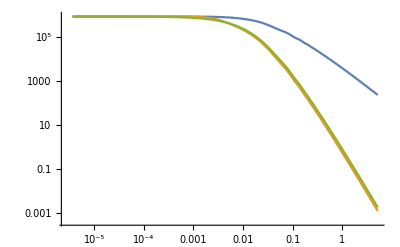

```mathematica
TkC30=Import[dir<>"nuFS1_transfer_out_z30.dat","Data"][[;;,{1,2}]];
Tknu30=Import[dir<>"nuFS1_transfer_out_z30.dat","Data"][[;;,{1,6}]];
koverhtab=Import[dir<>"nuFS1_transfer_out_z30.dat","Data"][[;;,1]];
len=Length[koverhtab];
mnu=0.1;(*eV*)
OmM=(.022+.12)/h/h;
αnu=1/(0.08 *mnu/0.1 Sqrt[OmM/.3]/Sqrt[1+30.]);

fnu[k_]:=1/(1+(αnu k))^2;

Tknufit30=Table[{koverhtab[[j]],TkC30[[j,2]] fnu[koverhtab[[j]]]},{j,1,len}];

ListLogLogPlot[{Abs@TkC30,Abs@Tknu30, Abs@Tknufit30},Joined->True]
```

fit from bode and Ostriker:

```mathematica
h=0.67;
Ωw=0.12/h/h;
mw=0.1;(*keV*)
gw=2 3/4; 

ΔNeff=(0.12 * 94.07/(1000 mw))^(4/3)
```

0.0545561

```mathematica
α=0.05 (Ωw/.4)^.15 (h/0.65)^1.3 (mw/1)^(-1.15) (gw/1.5)^(-.29);
f[k_]:=(1+(α k)^2)^(-5);
```

```mathematica
α=0.048 (Ωw/.4)^.15 (h/0.65)^1.3 (mw/1)^(-1.15) (gw/1.5)^(-.29);
ν=1.2;
f[k_]:=(1+(α k)^(2 ν))^(-5/ν);
```

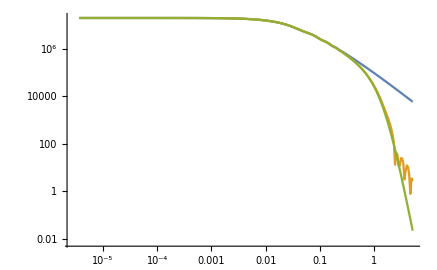

```mathematica
koverhtab=Import[dir<>"_transfer_out_z0.dat","Data"][[;;,1]];
len=Length[koverhtab];
TkLWDMfit=Table[{koverhtab[[j]],TkLCDM[[j,2]] f[koverhtab[[j]]]},{j,1,len}];
ListLogLogPlot[{Abs@TkLCDM,Abs@TkLWDM,Abs@TkLWDMfit},Joined->True]
```